```mathematica
SetDirectory["c:\\git\\fusor-stuff\\mcnp"];
Get["histogram.m"]
```

histogram package loaded - You will want to reset xRange and yRange

```mathematica
tallySn2404=getMcnpTallyFromClipboard[];
```

```mathematica
xRange={0,3 10^6};yRange=All;
```

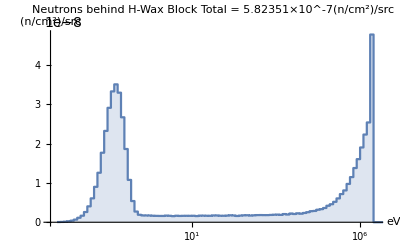

```mathematica
xRange={0,3 10^6};yRange=All;logFluenceHistWithTitle[tallySn2404,"Neutrons behind H-Wax Block"]
```

```mathematica
gmSnTally=getCsvTallyFromClipboard[];
```

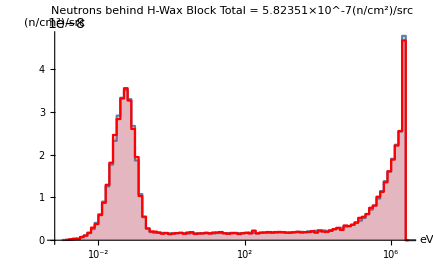

```mathematica
xRange={0,3 10^6};yRange=All;Show[logFluenceHistWithTitle[tallySn2404,"Neutrons behind H-Wax Block"],logFluenceHist[gmSnTally]]
```

```mathematica
tallySn2414=getMcnpTallyFromClipboard[];
```

```mathematica
xRange={0,0.15};
```

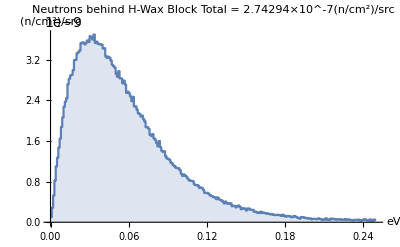

```mathematica
xRange={0,0.25};linearFluenceHistWithTitle[tallySn2414,"Neutrons behind H-Wax Block"]
```

```mathematica
gmSnThermalTally=getCsvTallyFromClipboard[];
```

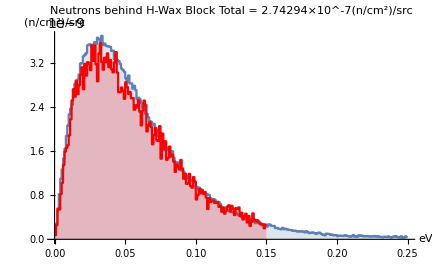

```mathematica
Show[linearFluenceHistWithTitle[tallySn2414,"Neutrons behind H-Wax Block"],linearFluenceHist[gmSnThermalTally]]
```

```mathematica
tallySn2424=getMcnpTallyFromClipboard[];
```

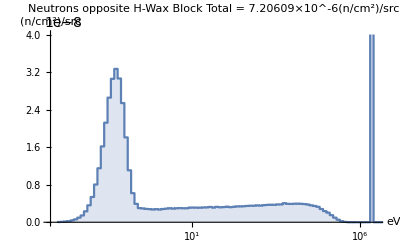

```mathematica
xRange={0,3 10^6};yRange={0,4.0 10^-8};logFluenceHistWithTitle[tallySn2424,"Neutrons opposite H-Wax Block"]
```

```mathematica
gmSnTallyOpp=getCsvTallyFromClipboard[];
```

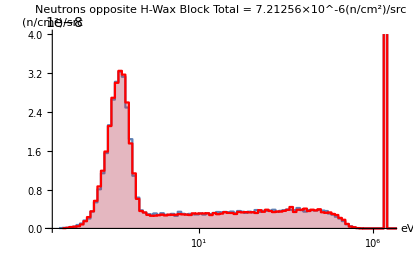

```mathematica
xRange={0,3 10^6};yRange={0,4.0 10^-8};Show[logFluenceHistWithTitle[tallySn2324,"Neutrons opposite H-Wax Block"],logFluenceHist[gmSnTallyOpp]]
```

```mathematica
tallySn2434=getMcnpTallyFromClipboard[];
```

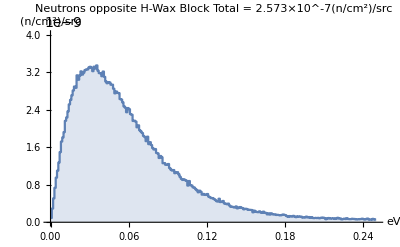

```mathematica
xRange={0,0.25};yRange={0,4 10^-9};linearFluenceHistWithTitle[tallySn2434,"Neutrons opposite H-Wax Block"]
```

```mathematica
gmSnThermalTallyOpp=getCsvTallyFromClipboard[];
```

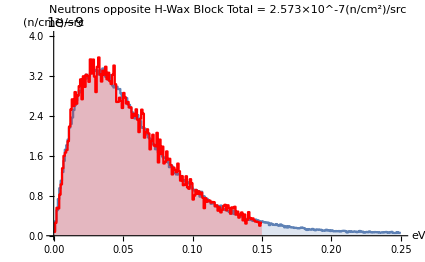

```mathematica
xRange={0,0.25};yRange={0,4 10^-9};Show[linearFluenceHistWithTitle[tallySn2434,"Neutrons opposite H-Wax Block"],linearFluenceHist[gmSnThermalTallyOpp]]
```